{{r→ConditionalExpression[2 √(d/(-1+d)^4)+(1+d)/(-1+d)^2, 0<d<1]}}

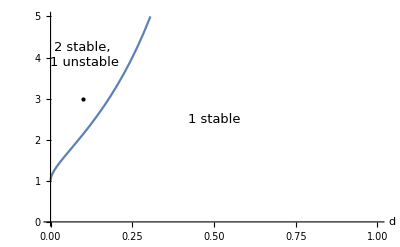

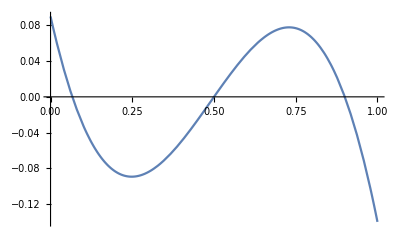

```mathematica
b = 1-d-n;

sol1 = Solve[ Sqrt[1-2(1+d)*r+(-1+d)^2*r^2] == 0, r];
sol1 = Solve[ Sqrt[1-2(1+d)*r+(-1+d)^2*r^2] == 0 && 1>((-1+r*(1-d)-Sqrt[1-2*(1+d)*r+(-1+d)^2*r^2]))/(2*r)>0 && 1>((-1+r*(1-d)+Sqrt[1-2*(1+d)*r+(-1+d)^2*r^2]))/(2*r)>0, r]

d0 = 0.1;
r0 = 3;

Plot[r/.sol1,{d,0,1},AxesLabel -> Automatic, PlotRange->{{0,1},{0,5}}, 
Epilog->{Text[Style["1 stable",13],Scaled[{0.5,0.5}]],
Text[Style["2 stable, \n1 unstable",13],Scaled[{0.12,0.8}]],
Point[{d0,r0}]}]
ndot =(d+n)*(1-d-n)-r*n*(1-d-n)^2;
Plot[ndot/.{d->d0, r-> r0},{n,0,1}]
```

```mathematica
hy
```

```mathematica
sol3 = Assuming[{1≥n≥0, r>0, 1≥d≥0}, Simplify[Solve[(d+n)*b - r*n*b^2 == 0, n]]]
Plot3D[n/.sol3, {d,0,1},{r,0,5}]
```

{{n→1-d},{n→-(1-r+d r+√(-4 d r+(1+(-1+d) r)^2))/(2 r)},{n→(-1+r-d r+√(-4 d r+(1+(-1+d) r)^2))/(2 r)}}

-Graphics3D-

{{r→ConditionalExpression[2 √(d/(-1+d)^4)+(1+d)/(-1+d)^2, 0<d<1]}}

```mathematica
Hysteresis -> Yes!
Catastrophes -> Yes!
```